# DYS HW3-3 Homoclinic bifurcation

-Graphics-

## a.) a) Using a numerical method of your choice, find the value where the system undergoes a homoclinic bifurcation. Give your result with two significant digits.

This point need to be

```mathematica
x'[t] == m * x[t] + y[t] - x[t]^2;
y'[t] == -x[t] + m * y[t] + 2 * x[t]^2;
```

```mathematica
(*ClearAll["Global'*"]
eq1 = m*x[t] + y[t] - x[t]^2 == 0;
eq2 = -x[t] + m*y[t] + 2*x[t]^2 == 0;

xStar = (1+m^2)/(m+2);
yStar = (1/m) * (xStar - 2*xStar^2) // Expand // Simplify

detFP2 = ((m-2*xStar) * (m)) - ((-1 + 4* xStar)*(1));

Solve[((m - 2*xStar)*m) - ((-1 + 4*xStar)*1) == 1, m];

A = {{m - 2 * xStar, 1},{-1+4*xStar, 2 * xStar}};
DetA = Det[A] 
r = DetA /. m->-1

TraceA = Trace[A] // Simplify;
sol = NSolve[DetA[[1]] == 0,m] // Simplify

(1-2*u + u^2 - 2*u^3)/(2+u)^2*)
```

Implemented in a numerical solving in Python. With the manipulate plot below, are range for \mu_{critical} could be found. In the diff. equation is computed and evaluated at time = 0 and time = 100. Time 100 is truly just a arbitrary number that in the end gave a okayish solution. The two evaluated points are compared with each other and if the distance is smaller than a certain threshold, it is assumed that the critical \mu got found.
-Graphics-
-Graphics-

```mathematica
ClearAll["Global'*"]

Manipulate[
  StreamPlot[{u*x + y - x^2, -x + u*y + 2x^2}, {x, -1, 1}, {y, -1, 1}, 
    PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black), StreamScale->Tiny, 
    StreamStyle -> Directive[Black]],
  {{u, 0.066, "u"}, 0.05, .07, 0.001}
]
```

## b.) b) Plot the phase portraits that occur for the cases m < 0, m=0, 0< m < m_c , m = m_c and m > m_c, marking and labelling fixed points, closed orbits, limit cycles and homoclinic orbits. Use a numerical solver, for example NDSolve|| in Mathematica (using StreamPlot] will not give enough resolution for this task). Upload the portraits as .png images or as .pdf. -Graphics-

0.41

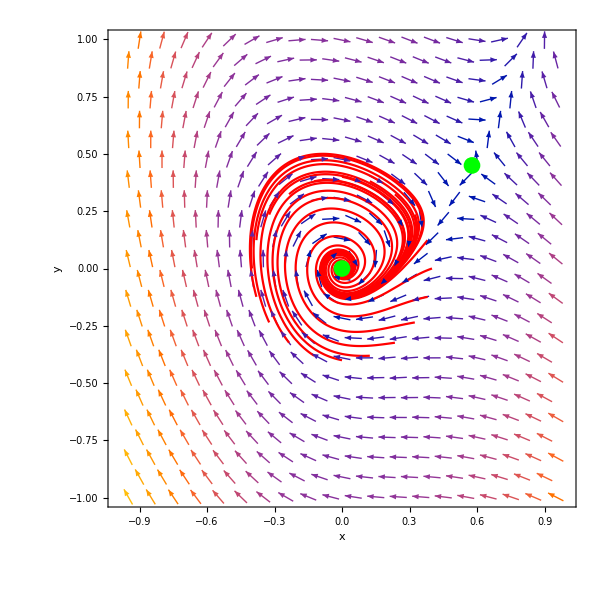

```mathematica
ClearAll["Global`*"]

u = -0.2;

Equation1 = x'[t] == u*x[t] + y[t] - x[t]^2;
Equation2 = y'[t] == -x[t] + u*y[t] + 2*x[t]^2;

System1 = {Equation1, Equation2};

FixPoint1 = {0, 0};
FixPoint2 = {(1 + u^2)/(u + 2), (1-2*u + u^2 - 2*u^3)/(2+u)^2} // Expand // Simplify;

t0 = 0;
tMax = 50;

(* Place init points around the FP*) 
numInitPoints = 20;
radiusMin = 0.4;
radiusMax = radiusMin + 0.01

initialPoints = Table[
   {x[0] == FixPoint1[[1]] + radius*Cos[2 Pi k/numInitPoints], 
    y[0] == FixPoint1[[2]] + radius*Sin[2 Pi k/numInitPoints]},
   {radius, Range[radiusMin, radiusMax, 1]},
   {k, numInitPoints}
];

(* Flatten the list to get a single list of initial points *)
initialPoints = Flatten[initialPoints, 1];

(* Use NDSolve for each initial point and store the solutions in a list *)
solutions = Table[NDSolve[{System1, initialPoints[[i]]}, {x, y}, {t, t0, tMax}], {i, Length[initialPoints]}];

(* Plot the trajectories for each solution with arrows indicating the direction *)
TrajectoryPlotArrows = Table[
   ParametricPlot[Evaluate[{x[t], y[t]} /. solution], {t, t0, tMax}, PlotStyle -> Red],
   {solution, solutions}
];

(* Add arrows indicating the direction using VectorPlot *)
VectorPlotArrows = VectorPlot[{u*x + y - x^2, -x + u*y + 2*x^2}, {x, -1, 1}, {y, -1, 1},
   VectorPoints -> 20, VectorScale -> 0.03, VectorStyle -> Directive[Black]];

(* Show the combined plot *)
Show[VectorPlotArrows, TrajectoryPlotArrows, FrameLabel -> {"x", "y"}, 
  PlotLabel -> "", ImageSize -> 600,
  Epilog -> {Green, PointSize[0.02], {Point[{FixPoint2[[1]], FixPoint2[[2]]}],Point[{FixPoint1[[1]], FixPoint1[[2]]}]}}]
```

-Graphics-

0.21

NDSolve::nderr: Error test failure at t == 28.2351; unable to continue.

NDSolve::nderr: Error test failure at t == 28.0104; unable to continue.

NDSolve::nderr: Error test failure at t == 27.926; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

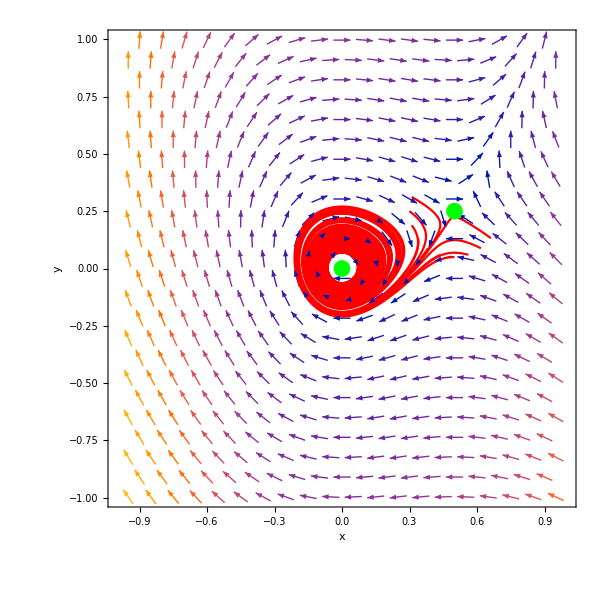

```mathematica
ClearAll["Global`*"]

u = 0;

Equation1 = x'[t] == u*x[t] + y[t] - x[t]^2;
Equation2 = y'[t] == -x[t] + u*y[t] + 2*x[t]^2;

System1 = {Equation1, Equation2};

FixPoint1 = {0, 0};
FixPoint2 = {(1 + u^2)/(u + 2), (1-2*u + u^2 - 2*u^3)/(2+u)^2} // Expand // Simplify;

t0 = 0;
tMax = 200;

(* Place init points around the FP*) 
numInitPoints = 20;
radiusMin = 0.2;
radiusMax = radiusMin + 0.01

initialPoints = Table[
   {x[0] == FixPoint2[[1]] + radius*Cos[2 Pi k/numInitPoints], 
    y[0] == FixPoint2[[2]] + radius*Sin[2 Pi k/numInitPoints]},
   {radius, Range[radiusMin, radiusMax, 1]},
   {k, numInitPoints}
];

(* Flatten the list to get a single list of initial points *)
initialPoints = Flatten[initialPoints, 1];

(* Use NDSolve for each initial point and store the solutions in a list *)
solutions = Table[NDSolve[{System1, initialPoints[[i]]}, {x, y}, {t, t0, tMax}], {i, Length[initialPoints]}];

(* Plot the trajectories for each solution with arrows indicating the direction *)
TrajectoryPlotArrows = Table[
   ParametricPlot[Evaluate[{x[t], y[t]} /. solution], {t, t0, tMax}, PlotStyle -> Red],
   {solution, solutions}
];

(* Add arrows indicating the direction using VectorPlot *)
VectorPlotArrows = VectorPlot[{u*x + y - x^2, -x + u*y + 2*x^2}, {x, -1, 1}, {y, -1, 1},
   VectorPoints -> 20, VectorScale -> 0.03, VectorStyle -> Directive[Black]];

(* Show the combined plot *)
Show[VectorPlotArrows, TrajectoryPlotArrows, FrameLabel -> {"x", "y"}, 
  PlotLabel -> "", ImageSize -> 600,
  Epilog -> {Green, PointSize[0.02], {Point[{FixPoint2[[1]], FixPoint2[[2]]}],Point[{FixPoint1[[1]], FixPoint1[[2]]}]}}]
```

-Graphics-

0.21

NDSolve::nderr: Error test failure at t == 27.9101; unable to continue.

NDSolve::nderr: Error test failure at t == 27.7643; unable to continue.

NDSolve::nderr: Error test failure at t == 27.7359; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

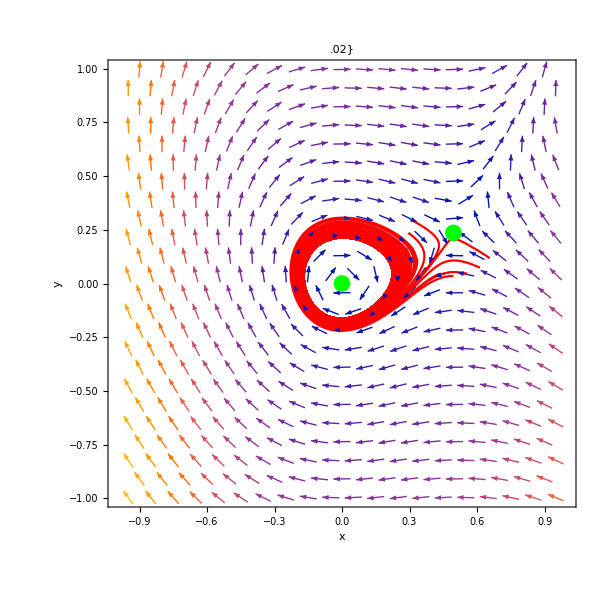

```mathematica
ClearAll["Global`*"]

u = 0.02;

Equation1 = x'[t] == u*x[t] + y[t] - x[t]^2;
Equation2 = y'[t] == -x[t] + u*y[t] + 2*x[t]^2;

System1 = {Equation1, Equation2};

FixPoint1 = {0, 0};
FixPoint2 = {(1 + u^2)/(u + 2), (1-2*u + u^2 - 2*u^3)/(2+u)^2} // Expand // Simplify;

t0 = 0;
tMax = 200;

(* Place init points around the FP*) 
numInitPoints = 20;
radiusMin = 0.2;
radiusMax = radiusMin + 0.01

initialPoints = Table[
   {x[0] == FixPoint2[[1]] + radius*Cos[2 Pi k/numInitPoints], 
    y[0] == FixPoint2[[2]] + radius*Sin[2 Pi k/numInitPoints]},
   {radius, Range[radiusMin, radiusMax, 1]},
   {k, numInitPoints}
];

(* Flatten the list to get a single list of initial points *)
initialPoints = Flatten[initialPoints, 1];

(* Use NDSolve for each initial point and store the solutions in a list *)
solutions = Table[NDSolve[{System1, initialPoints[[i]]}, {x, y}, {t, t0, tMax}], {i, Length[initialPoints]}];

(* Plot the trajectories for each solution with arrows indicating the direction *)
TrajectoryPlotArrows = Table[
   ParametricPlot[Evaluate[{x[t], y[t]} /. solution], {t, t0, tMax}, PlotStyle -> Red],
   {solution, solutions}
];

(* Add arrows indicating the direction using VectorPlot *)
VectorPlotArrows = VectorPlot[{u*x + y - x^2, -x + u*y + 2*x^2}, {x, -1, 1}, {y, -1, 1},
   VectorPoints -> 20, VectorScale -> 0.03, VectorStyle -> Directive[Black]];

(* Show the combined plot *)
Show[VectorPlotArrows, TrajectoryPlotArrows, FrameLabel -> {"x", "y"}, 
  PlotLabel -> ".02}", ImageSize -> 600,
  Epilog -> {Green, PointSize[0.02], {Point[{FixPoint2[[1]], FixPoint2[[2]]}],Point[{FixPoint1[[1]], FixPoint1[[2]]}]}}]
```

-Graphics-

0.0501

NDSolve::nderr: Error test failure at t == 29.2081; unable to continue.

NDSolve::nderr: Error test failure at t == 44.7496; unable to continue.

NDSolve::nderr: Error test failure at t == 29.7786; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

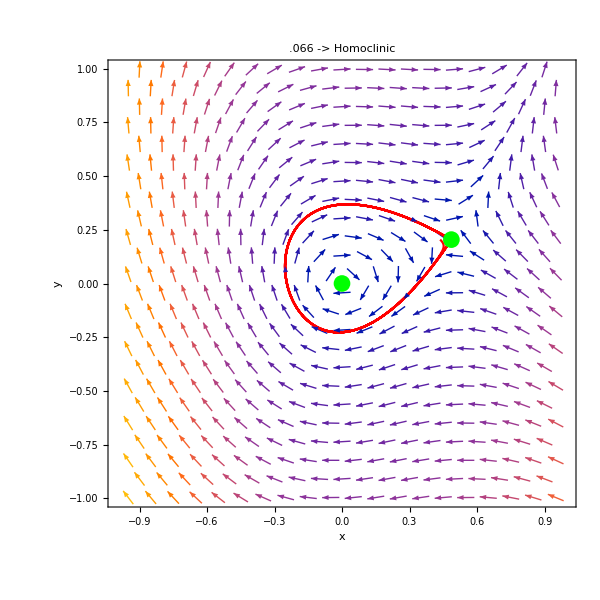

```mathematica
ClearAll["Global`*"]

u = 0.066;

Equation1 = x'[t] == u*x[t] + y[t] - x[t]^2;
Equation2 = y'[t] == -x[t] + u*y[t] + 2*x[t]^2;

System1 = {Equation1, Equation2};

FixPoint1 = {0, 0};
FixPoint2 = {(1 + u^2)/(u + 2), (1-2*u + u^2 - 2*u^3)/(2+u)^2} // Expand // Simplify;

t0 = 0;
tMax = 100;

(* Place init points around the FP*) 
numInitPoints = 4;
radiusMin = 0.05;
radiusMax = radiusMin + 0.0001

initialPoints = Table[
   {x[0] == FixPoint2[[1]] + radius*Cos[2 Pi k/numInitPoints], 
    y[0] == FixPoint2[[2]] + radius*Sin[2 Pi k/numInitPoints]},
   {radius, Range[radiusMin, radiusMax, 1]},
   {k, numInitPoints}
];

(* Flatten the list to get a single list of initial points *)
initialPoints = Flatten[initialPoints, 1];

(* Use NDSolve for each initial point and store the solutions in a list *)
solutions = Table[NDSolve[{System1, initialPoints[[i]]}, {x, y}, {t, t0, tMax}], {i, Length[initialPoints]}];

(* Plot the trajectories for each solution with arrows indicating the direction *)
TrajectoryPlotArrows = Table[
   ParametricPlot[Evaluate[{x[t], y[t]} /. solution], {t, t0, tMax}, PlotStyle -> Red],
   {solution, solutions}
];

(* Add arrows indicating the direction using VectorPlot *)
VectorPlotArrows = VectorPlot[{u*x + y - x^2, -x + u*y + 2*x^2}, {x, -1, 1}, {y, -1, 1},
   VectorPoints -> 20, VectorScale -> 0.03, VectorStyle -> Directive[Black]];

(* Show the combined plot *)
Show[VectorPlotArrows, TrajectoryPlotArrows, FrameLabel -> {"x", "y"}, 
  PlotLabel -> ".066 -> Homoclinic", ImageSize -> 600,
  Epilog -> {Green, PointSize[0.02], {Point[{FixPoint2[[1]], FixPoint2[[2]]}],Point[{FixPoint1[[1]], FixPoint1[[2]]}]}}]
```

-Graphics-

0.31

NDSolve::nderr: Error test failure at t == 26.179; unable to continue.

NDSolve::nderr: Error test failure at t == 27.2929; unable to continue.

NDSolve::nderr: Error test failure at t == 46.6858; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

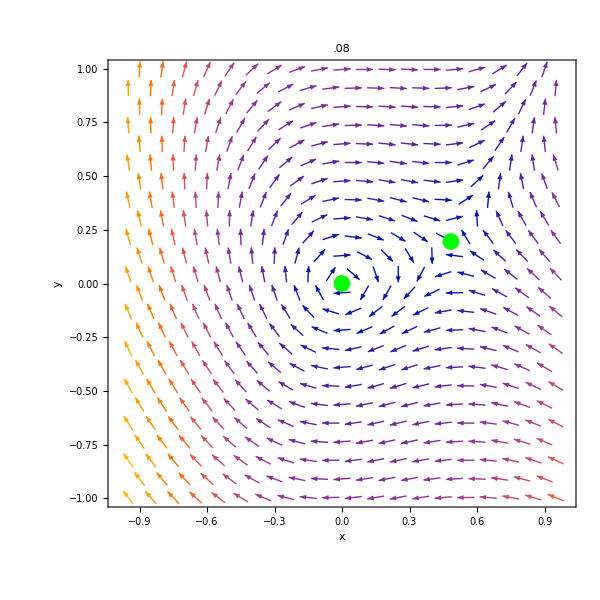

```mathematica
ClearAll["Global`*"]

u = 0.08;

Equation1 = x'[t] == u*x[t] + y[t] - x[t]^2;
Equation2 = y'[t] == -x[t] + u*y[t] + 2*x[t]^2;

System1 = {Equation1, Equation2};

FixPoint1 = {0, 0};
FixPoint2 = {(1 + u^2)/(u + 2), (1-2*u + u^2 - 2*u^3)/(2+u)^2} // Expand // Simplify;

t0 = 0;
tMax = 200;

(* Place init points around the FP*) 
numInitPoints = 6;
radiusMin = 0.3;
radiusMax = radiusMin + 0.01

initialPoints = Table[
   {x[0] == FixPoint2[[1]] + radius*Cos[2 Pi k/numInitPoints], 
    y[0] == FixPoint2[[2]] + radius*Sin[2 Pi k/numInitPoints]},
   {radius, Range[radiusMin, radiusMax, 1]},
   {k, numInitPoints}
];

(* Flatten the list to get a single list of initial points *)
initialPoints = Flatten[initialPoints, 1];

(* Use NDSolve for each initial point and store the solutions in a list *)
solutions = Table[NDSolve[{System1, initialPoints[[i]]}, {x, y}, {t, t0, tMax}], {i, Length[initialPoints]}];

(* Plot the trajectories for each solution with arrows indicating the direction *)
TrajectoryPlotArrows = Table[
   ParametricPlot[Evaluate[{x[t], y[t]} /. solution], {t, t0, tMax}, PlotStyle -> Red],
   {solution, solutions}
];

(* Add arrows indicating the direction using VectorPlot *)
VectorPlotArrows = VectorPlot[{u*x + y - x^2, -x + u*y + 2*x^2}, {x, -1, 1}, {y, -1, 1},
   VectorPoints -> 20, VectorScale -> 0.03, VectorStyle -> Directive[Black]];

(* Show the combined plot *)
Show[VectorPlotArrows, TrajectoryPlotArrows, FrameLabel -> {"x", "y"}, 
  PlotLabel -> ".08", ImageSize -> 600,
  Epilog -> {Green, PointSize[0.02], {Point[{FixPoint2[[1]], FixPoint2[[2]]}],Point[{FixPoint1[[1]], FixPoint1[[2]]}]}}]
```

-Graphics-

FP1 is referred to the FP at {0,0}, FP2 the one depending on mu.

## c.) Find an analytical expression for the time t_1 to escape from the saddle to x(t_1)=1. -Graphics--Graphics-

Idea is to find a solution for x(t) and y(t), depending on m and g, and integrate from t = 0 to t = t1 until x(t1) == 1

```mathematica
ClearAll["Global`*"]

A = {{m - 2*x, 1},{-1+4*x, m}}
DetA = Det[A]
EigVal = Eigenvalues[A] // Simplify
EigVec = Eigenvectors[A]
```

{{m-2 x,1},{-1+4 x,m}}

1+m^2-4 x-2 m x

{m-x-√(-1+4 x+x^2),m-x+√(-1+4 x+x^2)}

{{-(x+√(-1+4 x+x^2))/(-1+4 x),1},{-(x-√(-1+4 x+x^2))/(-1+4 x),1}}

-Graphics-

## d.) Find an analytical expression for u suitable for the system in EQ(1)

Find u in terms of . For this find the unstable Eigenvector (where Eigenvalue is > 0). Evaluate the Jacobian at the FP xStar(\mu)

```mathematica
ClearAll["Global`*"]

xStar = (1+m^2)/(m+2);
A = {{m - 2 * x, 1},{4 * x-1, m}} 

(* Eigenvalues *)
EigVal = Eigenvalues[A] /. x->xStar //Simplify
(* EigVec = Eigenvectors[A] // Simplify *)
```

{{m-2 x,1},{-1+4 x,m}}

{m-1/(2+m)-m^2/(2+m)-√((5+9 m^2+4 m^3+m^4)/(2+m)^2),m-1/(2+m)-m^2/(2+m)+√((5+9 m^2+4 m^3+m^4)/(2+m)^2)}

## e.) -Graphics-

-Graphics-